```mathematica
filesAR=FileNames["/home/carla/GDC/DLB/GDC_Conf_AR_DLB_DOJ_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/DLB/GDC_Conf_BR_DLB_DOJ_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{1.,1,1},{1.,1,1},{0.000765111,1,1307},{0.00609756,1,164},{0.00714286,5,700},{0.00390625,5,1280},{0.0223325,9,403},{0.025641,9,351},{1.,1,1}}

{{1.,160,160},{1.,7,7},{0.000765111,1,1307},{0.00609756,101,16564},{0.00403226,78,19344},{0.000821732,1300,1582025},{0.00618132,9,1456},{0.025641,3,117}}

```mathematica
dojAR=confAR[[All,1]]
dojBR=confBR[[All,1]]
```

{1.,1.,0.000765111,0.00609756,0.00714286,0.00390625,0.0223325,0.025641,1.}

{1.,1.,0.000765111,0.00609756,0.00403226,0.000821732,0.00618132,0.025641}

```mathematica
sList={0,1,2,3,4,5,6,7,8};
sList2={0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&, ran2];
```

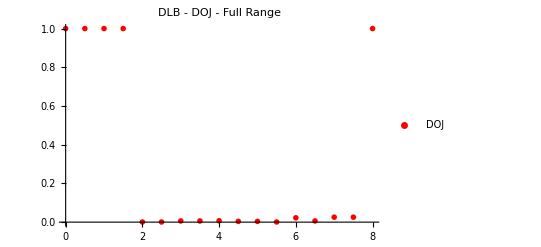

```mathematica
PlotDOJAllParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"DLB - DOJ - Full Range", PlotMarkers->{{"D",12}}]
```

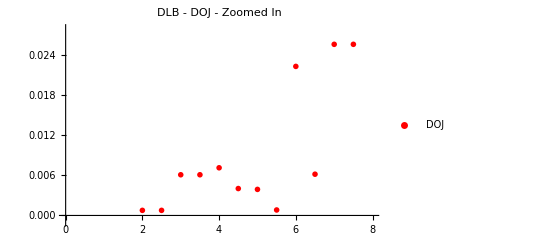

```mathematica
PlotDOJParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->{-0.001, 0.028},  PlotLabel->"DLB - DOJ - Zoomed In",  PlotMarkers->{{"D",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/DLB/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"DLB_DOJ.txt"]
Export["DLB_DOJ.jpeg",PlotDOJAllParts,ImageSize->850]
Export["DLB_DOJ_Zoomed_In.jpeg",PlotDOJParts,ImageSize->850]
```

DLB_DOJ.jpeg

DLB_DOJ_Zoomed_In.jpeg